```mathematica
(* Computer Graphics with Applications of Dr. Makhanov. (Google's Version) *)
```

```mathematica
(* Lecture 11: Matrix Algebra and Geometric Transformations *)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D, DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot}, ImageSize->Medium,AxesLabel->{"x","y","z"}];
```

```mathematica
(* Matrix Algebra *)
```

```mathematica
(* Example 1 Rotate a point around  Paround=(-5,-5) at the radius RR=3.5 *)
```

```mathematica
RR1={0,3.5};
```

```mathematica
Paround1={-5,-5};
```

```mathematica
(* Point1 {0,0} in the H-coordinates  *)
```

```mathematica
PointH1={0,0,1};
```

```mathematica
(* Getting the rotation matrix (3 steps)  *)
```

```mathematica
RP1=Composition[TranslationTransform[Paround1],RotationTransform[a],TranslationTransform[RR1]]
```

TransformationFunction[(1. Cos[a] | -1. Sin[a] | -5.-3.5 Sin[a]
1. Sin[a] | 1. Cos[a] | -5.+3.5 Cos[a]
0 | 0 | 1.)]

```mathematica
MP1=TransformationMatrix[RP1]
```

{{1. Cos[a],-1. Sin[a],-5.-3.5 Sin[a]},{1. Sin[a],1. Cos[a],-5.+3.5 Cos[a]},{0,0,1.}}

```mathematica
MFP1[a_]:=Evaluate[MP1]
```

```mathematica
MatrixForm[MFP1[a]]
```

(1. Cos[a] | -1. Sin[a] | -5.-3.5 Sin[a]
1. Sin[a] | 1. Cos[a] | -5.+3.5 Cos[a]
0 | 0 | 1.)

```mathematica
(* Matrix-function PR1[t], where [[1;;2]] eliminates the H-component of PR1[t] (it is always =1)  *)
```

```mathematica
PR1[t_]:=(MFP1[t].PointH1)[[1;;2]]
```

```mathematica
MatrixForm[PR1[t]]
```

(-5.-3.5 Sin[t]
-5.+3.5 Cos[t])

```mathematica
(* Result *)
```

```mathematica
(* Center of rotation *)
```

```mathematica
PParound1:={PointSize[0.05],Red,Point[Paround1]}
```

```mathematica
(* Animation by PR1[t] *)
```

```mathematica
AnimPR1[t_]:=Graphics[{{PointSize[0.05],Point[PR1[t]]},PParound1},Axes->True,PlotRange->15]
```

```mathematica
Manipulate[AnimPR1[t],{t,0,2Pi}]
```

```mathematica
(* Example 1' Back to the geometric transforms. Let us solve the same problem using primitives *)
```

```mathematica
RR1={0,3.5};
```

```mathematica
Paround1={-5,-5};
```

```mathematica
(* Point1 {0,0} no H-coordinates ! *)
```

```mathematica
myPoint={0,0};
```

```mathematica
(* Transformation function *)
```

```mathematica
GT1[a_]:=GeometricTransformation[Point[myPoint],Composition[TranslationTransform[Paround1],RotationTransform[a],TranslationTransform[RR1]]]
```

```mathematica
(* Center of rotation *)
```

```mathematica
PParound1:={PointSize[0.05],Red,Point[Paround1]}
```

```mathematica
(* Animation by PR1[t] *)
```

```mathematica
myAnim1[t_]:=Graphics[{{PointSize[0.05],GT1[t]},PParound1},Axes->True,PlotRange->15]
```

```mathematica
Manipulate[myAnim1[t],{t,0,2Pi}]
```

```mathematica
(* Example 2' Alternative solution by primitives and a composed transform RotationTransform[a,Paround1] *)
```

```mathematica
RR1={0,3.5};
```

```mathematica
Paround1={-5,-5};
```

```mathematica
(* The original position of the our point is *)
```

```mathematica
Pinit1={-5,-5}+{0, 3.5}
```

{-5,-1.5}

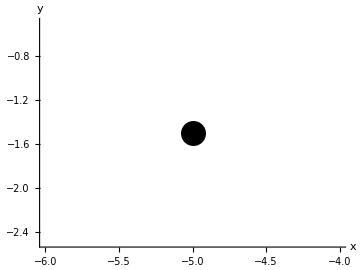

```mathematica
Graphics[{PointSize[0.05],Point[Pinit1]},Axes->True,PlotRange->15]
```

```mathematica
(* Let is Rotate this point around Paround using the rotation function Rotate[a,p] *)
```

```mathematica
GT1p[a_]:=GeometricTransformation[Point[Pinit1],Paround1]
```

```mathematica
(* We have *)
```

```mathematica
myAnim1p[t_]:=Graphics[{PointSize[0.05],GT1p[t],PParound1},Axes->True,PlotRange->15]
```

```mathematica
Manipulate[myAnim1p[t],{t,0,2Pi}]
```

```mathematica
(* Exercise 1: Solve problem 1 using Matrix Algebra using a single transform RotationTransform[a,Paround1] *)
```

```mathematica
(*Example 3 Rotate a vector object f[x_]:=x^2 for x={-1,1} around the origin using Matric Algebra *)
```

```mathematica
f2[x_]:=x^2
```

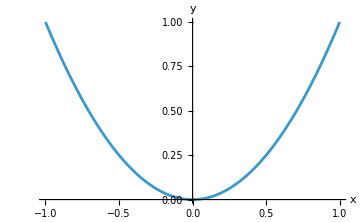

```mathematica
Plot[f2[t],{t,-1,1}]
```

```mathematica
RT2=RotationTransform[a]
```

TransformationFunction[(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)]

```mathematica
(* Rotation around the origin  *)
```

```mathematica
M2=TransformationMatrix[RT2]
```

{{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}

```mathematica
(* Convert the formula into the matrix-function *)
```

```mathematica
M2F[a_]:=Evaluate[M2]
```

```mathematica
(*Convert the explicit function y=f[x] into the parametric form in the H- coordinates   *)
```

```mathematica
S2H[t_]:={t, f2[t],1}
```

```mathematica
S2H[s]
```

{s,s^2,1}

```mathematica
(*  Example of i;;j - select a part of a list by index from i to j such as A[[i;;j]]  *)
```

```mathematica
{1,2,3,8,9,10}[[2;;4]]
```

{2,3,8}

```mathematica
(* Rotate and cut the H coordinate using ;; *)
```

```mathematica
PR2[a_,t_]:=(M2F[a].S2H[t])[[1;;2]]
```

```mathematica
MatrixForm[PR2[a,t]]
```

(t Cos[a]-t^2 Sin[a]
t^2 Cos[a]+t Sin[a])

```mathematica
(* Plot of the the rotated curve *)
```

```mathematica
p2[a_]:=ParametricPlot[PR2[a,t],{t,-1,1},PlotRange->1]
```

```mathematica
(*  Zero *)
```

```mathematica
Zero={Red,PointSize[0.05],Point[{0,0}]}
```

{RGBColor[1, 0, 0],PointSize[0.05],Point[{0,0}]}

```mathematica
Zero2=Graphics[Zero];
```

```mathematica
(*  Animate *)
```

```mathematica
p2All[t_]:=Show[p2[t],Zero2]
```

```mathematica
Manipulate[p2All[a],{a,0,2Pi}]
```

```mathematica
(* Example 4 Rotate a parametric curve 2{Sin[2t],Cos[3t]} around the point Paround5=5/2,5/2} with the angular speed a 
at the radius R5=3/2 and around itself with the angular speed b Use the primitive S5P *)
```

```mathematica
Clear[t]
```

```mathematica
Paround5={5/2,5/2};
```

```mathematica
RR5={0,3/2};
```

```mathematica
S5[t_]:=2{Sin[2t],Cos[3t]}
```

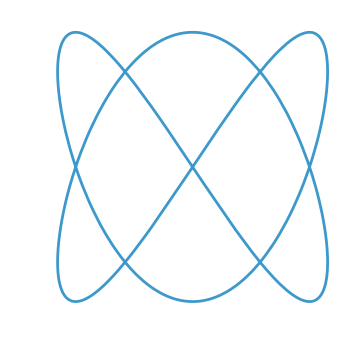

```mathematica
S5G=ParametricPlot[S5[t],{t,0,2Pi}, Axes->False]
```

```mathematica
(* Convert the graphics into the primitive, immediate assignment "=", important! S5P becomes a collection of primitives *)
```

```mathematica
S5P=S5G[[1]];
```

```mathematica
(* Check *)
```

```mathematica
Graphics[S5P]
```

-Graphics-

```mathematica
(* The object to be rotated *)
```

```mathematica
Object5={Zero,S5P};
```

```mathematica
(* Check  *)
```

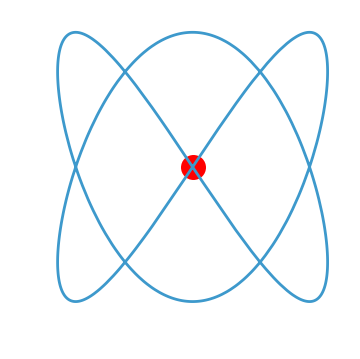

```mathematica
Graphics[Object5]
```

```mathematica
RT5[a_,b_]:=GeometricTransformation[Object5,Composition[RotationTransform[a,Paround5],TranslationTransform[RR5],RotationTransform[b]]];
```

```mathematica
GParound5={Purple,PointSize[0.05],Point[Paround5]};
```

```mathematica
ShowAll5[a_,b_]:=Graphics[{RT5[a,b],GParound5},PlotRange->7,Axes->True]
```

```mathematica
Manipulate[ShowAll5[a,b],{a,0,2Pi},{b,0,2Pi}]
```

```mathematica
(* To speed up a=b   *)
```

```mathematica
Manipulate[ShowAll5[a,a],{a,0,2Pi}]
```

```mathematica
(* Basic 2 and 3D Transformations *)
```

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```

```mathematica
(* Example 1 Graphics3D Primitives. Rotate a Torus[{x,y,z},R1,R2]  positioned at {0,0,0} around the y-axis : vector {0,1,0} 
and around a vector (0,0,1) anchored at {1,1,0}  *)
```

```mathematica
R1=1;R2=2;
```

```mathematica
Tor={Purple,Opacity[0.5],Torus[{0,0,0},{R1,R2}]};
```

```mathematica
Zero3={Red,PointSize[0.06],Point[{0,0,0}]};
```

```mathematica
(* Rotate around the Y-axis *)
```

```mathematica
Yrot=2{0,1,0};
```

```mathematica
ArY={Thick,Green,Arrow[{{0,0,0},Yrot}]}
```

{Thickness[Large],RGBColor[0, 1, 0],Arrow[{{0,0,0},{0,2,0}}]}

```mathematica
AllTor={Tor,Zero3,ArY}
```

{{RGBColor[0.5, 0, 0.5],Opacity[0.5],Torus[{0,0,0},{1,2}]},{RGBColor[1, 0, 0],PointSize[0.06],Point[{0,0,0}]},{Thickness[Large],RGBColor[0, 1, 0],Arrow[{{0,0,0},{0,2,0}}]}}

```mathematica
(*Check  *)
```

```mathematica
Graphics3D[AllTor,Axes->True, Boxed->True]
```

-Graphics3D-

```mathematica
Rot1Tor[a_]:=GeometricTransformation[AllTor,RotationTransform[a,Yrot]]
```

```mathematica
(*Check  *)
```

```mathematica
Graphics3D[Rot1Tor[Pi/2]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[Rot1Tor[a],PlotRange->2,Axes->True],{a,0,12Pi}]
```

```mathematica
(* Rotation around and around a vector Zrot=(0,0,1) ancored at Anc={2,2,0}  *)
```

```mathematica
Zrot=3{0,0,1};
```

```mathematica
An={2,2,0};
```

```mathematica
ArZ={Thick,Red,Arrow[{An,An+Zrot}]};
```

```mathematica
AllTorZ={Tor,Zero3,ArZ};
```

```mathematica
AllTor2={Tor,Zero3};
```

```mathematica
(* Check  *)
```

```mathematica
Graphics3D[{AllTor2,ArZ},Axes->True,Boxed->True]
```

-Graphics3D-

```mathematica
Rot2Tor[a_]:=GeometricTransformation[AllTor2,RotationTransform[a,Zrot,An]]
```

```mathematica
Manipulate[Graphics3D[{Zero3,ArZ,Rot2Tor[a]},PlotRange->{{-3,7},{-3,7},{-2,3}},Axes->True],{a,0,12Pi}]
```

```mathematica
(* Exercise Additionally rotate the Torus around its center in the Y direction *)
```

```mathematica
Rot3Tor[a_]:=GeometricTransformation[AllTor2,Composition[RotationTransform[a,Zrot,An], RotationTransform[6a,Yrot]]]
```

```mathematica
Manipulate[Graphics3D[{Zero3,ArZ,Rot3Tor[a]},PlotRange->{{-3,7},{-3,7},{-5,5}},Axes->True],{a,0,2Pi}]
```

```mathematica
(* Example 2 3D Matrix Algebra. Rotation Matrices. rotate a surface f[x,y]=x^2-y^2 around the direction {0,0,1}- the z-axes anchored at the origin {0,0,0})  *)
```

```mathematica
f6[x_,y_]:=x^2-y^2
```

```mathematica
(* Convert into the parametric surface represented in the H-coordinates) *)
```

```mathematica
S6[u_,v_]:={u,v,f6[u,v],1}
```

```mathematica
ZeroH:={0,0,0}
```

```mathematica
RTza6=RotationTransform[a,{0,0,1}];
```

```mathematica
MCza6=TransformationMatrix[RTza6];
```

```mathematica
FCza6[a_]:=Evaluate[MCza6];
```

```mathematica
MatrixForm[FCza6[a]]
```

(Cos[a] | -Sin[a] | 0 | 0
Sin[a] | Cos[a] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
RotS6[u_,v_,a_]:=(FCza6[a].S6[u,v])[[1;;3]]
```

```mathematica
MatrixForm[RotS6[u,v,a]]
```

(u Cos[a]-v Sin[a]
v Cos[a]+u Sin[a]
u^2-v^2)

```mathematica
GZero3=Graphics3D[{Red,PointSize[0.1],Point[{0,0,0}]}];
```

```mathematica
GRotS6[a_]:=ParametricPlot3D[RotS6[u,v,a],{u,-1,1},{v,-1,1},PlotRange->1.5]
```

```mathematica
Manipulate[Show[GRotS6[a],GZero3],{a,0,2Pi}]
```

```mathematica
(* Example 3 (Graphics 3D, primitives) Translate along the knot {3/4t(t^2-4)(t^2-11),t^4-12t^2,1/30 t(t^2-1)(t^2-3)(t^2-9)(t^2-12)}  rotating around z *)
```

```mathematica
Ftra[t_]:={3/4t(t^2-4)(t^2-11),t^4-12t^2,1/30 t(t^2-1)(t^2-3)(t^2-9)(t^2-12)}
```

```mathematica
(* Translate along the knot {3/4t(t^2-4)(t^2-11),t^4-12t^2,1/30 t(t^2-1)(t^2-3)(t^2-9)(t^2-12)}  rotating around z *)
```

```mathematica
TrajCube=ParametricPlot3D[Ftra[t],{t,-3.5,3.5},Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
(* Convert into primitives *)
```

```mathematica
TrajCubeP=TrajCube[[1]];
```

```mathematica
RotTra[t_,a_]:=Composition[TranslationTransform[Ftra[t]],RotationTransform[a,{0,0,1}]];
```

```mathematica
CubeTrans[t_,a_]:=GeometricTransformation[Cube[10],RotTra[t,a]]
```

```mathematica
ShowFlyCube[t_,a_]:=Graphics3D[{CubeTrans[t,a],TrajCubeP},PlotRange->40,Axes->True]
```

```mathematica
Manipulate[ShowFlyCube[t,a],{t,-3.5,3},{a,0,2Pi}]
```

```mathematica
(* Simplify a=t *)
```

```mathematica
Manipulate[ShowFlyCube[t,t],{t,-3.5,3}]
```